# Testing out DMFormFactor functions

```mathematica
<<"v6/dmformfactor-V6.m";
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

## Event rate

Model setup

```mathematica
(* Model Setup *)
SetJChi[1/2](* WIMP spin *)
SetMChi[MWIMP GeV] (* WIMP mass in GeV *)
Xe131filename="default";  (* nuclear density matrix (using default density matrices) *)
bFM="default"; (* oscillation parameter (default: approximate formulae used) *)
SetIsotope[54,131,bFM,Xe131filename] (*[Z,A,bFM,filename]*)
SetCoeffsNonrel[3,3.1,"p"](* Set non-zero NR EFT coefficient values *)
```

Getting default matrix...

Setting isotope to xenon-131.

Matrix elements

```mathematica
TransitionProbability[v,qGeV](* Spin-averaged matrix element squared *)
```

Your Lagrangian is

L_prot=(3.95945×10^-9 χ̄χN̄N)/GeV^2

L_neut=(3.95945×10^-9 χ̄χN̄N)/GeV^2

Your transition probability is

1/GeV^4 ⅇ^(-67.4762 qGeV^2) (2.69015×10^-13-3.62113×10^-11 qGeV^2+1.92276×10^-9 qGeV^4-5.23867×10^-8 qGeV^6+8.08968×10^-7 qGeV^8-7.35075×10^-6 qGeV^10+0.000039221 qGeV^12-0.000117443 qGeV^14+0.000175642 qGeV^16-0.0000994134 qGeV^18+0.0000184195 qGeV^20)

```mathematica
TransitionProbability[v,qGeV,True] (* as above, with relativistic normalisation *)
```

Your Lagrangian is

L_prot=0.+(0.0000545076 ⅈ S_N·(q×v^⊥))/GeV^3

L_neut=0.

Your transition probability is

ⅇ^(-39.8764 qGeV^2) qGeV^2 (-0.393037 qGeV^10+0.00852433 v^2+qGeV^6 (0.0134931-81.4917 v^2)+qGeV^2 (0.00040821-0.456613 v^2)+qGeV^4 (-0.00604702+9.15739 v^2)+qGeV^8 (0.117966+271.513 v^2))

Differential cross section per recoil
energy

```mathematica
DiffCrossSection[]
```

Attempting to compute a recoil spectrum...

```mathematica
(* Parameters *)
mNucleon=0.938 GeV;
NT=1/(131 mNucleon);(*Number of target nuclei per detector mass*)
Centimeter=(10^13 Femtometer);
rhoDM=0.3GeV/Centimeter^3;(*Local dark matter density*)
ve=232 KilometerPerSecond;(*Earth's velocity in galactic rest frame*)
v0=220 KilometerPerSecond;(*Mean WIMP speed in galactic rest frame*)
SetHALO["MB"];(*using default MB Halo*)
```

```mathematica
(* Switch to cutoff MB Halo *)
vesc=550 KilometerPerSecond;
SetHALO["MBcutoff"];
```

```mathematica
dEdR=EventRate[NT,rhoDM,qGeV,ve,v0]
```

Your Lagrangian is

L_prot=0.+(0.0000545076 ⅈ S_N·(q×v^⊥))/GeV^3

L_neut=0.

Your event rate is

1/(GeV MWIMP^3)2.6053×10^-44 (0.000733832 ⅇ^(-67.4762 qGeV^2) (6.05768×10^-13 MWIMP^2 qGeV^2-1.5772×10^-10 MWIMP^2 qGeV^4+9.21011×10^-9 MWIMP^2 qGeV^6+3.00584×10^-7 MWIMP^2 qGeV^8-4.6939×10^-6 MWIMP^2 qGeV^10-0.000271272 MWIMP^2 qGeV^12+0.0061777 MWIMP^2 qGeV^14-0.0414371 MWIMP^2 qGeV^16+0.0889482 MWIMP^2 qGeV^18-1.00345×10^-6 MWIMP^2 qGeV^20+2.98027×10^-12 MWIMP^2 qGeV^22) (2.58109×10^-65 ⅇ^(-2 (1.11207+(30.7289 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP^2))) (-30 ⅇ^(144.+(-1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))^2) (-1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))+30 ⅇ^(144.+(1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))^2) (1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))+4.21818 ⅇ^(2 (1.11207+(30.7289 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP^2))) (-1611.26-15 (21026.-(944.264 (122.914 GeV+GeV MWIMP)^4 qGeV^4)/(GeV^4 MWIMP^4)))+85.7194 ⅇ^(144.+2 (1.11207+(30.7289 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP^2))) (Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]+Erf[1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])) UnitStep[10.9455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]-2.58109×10^-65 ⅇ^(-1.11207-(30.7289 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP^2)) (2 ⅇ^(1.11207+(30.7289 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP^2)) (1.01449×10^6-(246995. (122.914 GeV+GeV MWIMP)^3 qGeV^3)/(GeV^3 MWIMP^3)+(31406.4 (122.914 GeV+GeV MWIMP)^5 qGeV^5)/(GeV^5 MWIMP^5)+11.1207 (3492.+(170.341 (122.914 GeV+GeV MWIMP)^3 qGeV^3)/(GeV^3 MWIMP^3))+15.8182 (21026.-(944.264 (122.914 GeV+GeV MWIMP)^4 qGeV^4)/(GeV^4 MWIMP^4)))+5.18199×10^63 (-2 ⅇ^((11.6915 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)) (1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))+5.71463 ⅇ^(1.11207+(30.7289 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP^2)) (-1.-Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]))) UnitStep[13.0545-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP),-10.9455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])+1362.71 ⅇ^(-67.4762 qGeV^2) (0.-1.51442×10^-13 qGeV^4-2.4642×10^-15 MWIMP qGeV^4+1.24551×10^-6 MWIMP^2 qGeV^4+3.943×10^-11 qGeV^6+6.41589×10^-13 MWIMP qGeV^6-0.000100903 MWIMP^2 qGeV^6-2.30253×10^-9 qGeV^8-3.74658×10^-11 MWIMP qGeV^8+0.0031335 MWIMP^2 qGeV^8-7.5146×10^-8 qGeV^10-1.22275×10^-9 MWIMP qGeV^10-0.0473222 MWIMP^2 qGeV^10+1.17348×10^-6 qGeV^12+1.90943×10^-8 MWIMP qGeV^12+0.369471 MWIMP^2 qGeV^12+0.0000678179 qGeV^14+1.10351×10^-6 MWIMP qGeV^14-1.42699 MWIMP^2 qGeV^14-0.00154443 qGeV^16-0.0000251303 MWIMP qGeV^16+2.15487 MWIMP^2 qGeV^16+0.0103593 qGeV^18+0.000168562 MWIMP qGeV^18-3.05661×10^-6 MWIMP^2 qGeV^18-0.022237 qGeV^20-0.000361832 MWIMP qGeV^20-1.47189×10^-6 MWIMP^2 qGeV^20+2.50863×10^-7 qGeV^22+4.08194×10^-9 MWIMP qGeV^22+1.66049×10^-11 MWIMP^2 qGeV^22-7.45068×10^-13 qGeV^24-1.21234×10^-14 MWIMP qGeV^24-4.93169×10^-17 MWIMP^2 qGeV^24) (-2.58109×10^-64 (-4.21818 (-433.888+(92.1866 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP^2))+1.83697×10^63 (-Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]-Erf[1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])) UnitStep[10.9455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]-2.58109×10^-64 (2 (13.0545-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)) (3+(13.0545-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)) (22.9455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)))+1.83697×10^63 (-1.-Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])) UnitStep[13.0545-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP),-10.9455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]))

```mathematica
dEdRsimp=Simplify[dEdR,{Element[GeV,Reals],GeV>0,Element[MWIMP,Reals],MWIMP>0,Element[qGeV,Reals],qGeV>0}]
```

1/(GeV MWIMP^3)2.6053×10^-44 ⅇ^(-67.4762 qGeV^2) (1/MWIMP^3 1362.71 qGeV^4 (-1.51442×10^-13+3.943×10^-11 qGeV^2-2.30253×10^-9 qGeV^4-7.5146×10^-8 qGeV^6+1.17348×10^-6 qGeV^8+0.0000678179 qGeV^10-0.00154443 qGeV^12+0.0103593 qGeV^14-0.022237 qGeV^16+2.50863×10^-7 qGeV^18-7.45068×10^-13 qGeV^20+MWIMP (-2.4642×10^-15+6.41589×10^-13 qGeV^2-3.74658×10^-11 qGeV^4-1.22275×10^-9 qGeV^6+1.90943×10^-8 qGeV^8+1.10351×10^-6 qGeV^10-0.0000251303 qGeV^12+0.000168562 qGeV^14-0.000361832 qGeV^16+4.08194×10^-9 qGeV^18-1.21234×10^-14 qGeV^20)+MWIMP^2 (1.24551×10^-6-0.000100903 qGeV^2+0.0031335 qGeV^4-0.0473222 qGeV^6+0.369471 qGeV^8-1.42699 qGeV^10+2.15487 qGeV^12-3.05661×10^-6 qGeV^14-1.47189×10^-6 qGeV^16+1.66049×10^-11 qGeV^18-4.93169×10^-17 qGeV^20)) (1.00368×10^-61 MWIMP (-4.70663 MWIMP^2+15107.8 qGeV^2+245.827 MWIMP qGeV^2+1. MWIMP^2 qGeV^2+4.72398×10^60 MWIMP^2 Erf[1.05455+(-5.54336-681.355/MWIMP) qGeV]+4.72398×10^60 MWIMP^2 Erf[1.05455+5.54336 qGeV+(681.355 qGeV)/MWIMP]) UnitStep[10.9455+(-5.54336-681.355/MWIMP) qGeV]-8.79332×10^-62 (1.85695×10^6 qGeV^3+MWIMP qGeV^2 (-8622.11+45323.3 qGeV)+MWIMP^2 qGeV (-1726.63-140.295 qGeV+368.741 qGeV^2)+MWIMP^3 (-5.39202×10^60-14.0475 qGeV-0.570707 qGeV^2+1. qGeV^3)-5.39202×10^60 MWIMP^3 Erf[1.05455-5.54336 qGeV-(681.355 qGeV)/MWIMP]) UnitStep[13.0545+(-5.54336-681.355/MWIMP) qGeV,-10.9455+(5.54336+681.355/MWIMP) qGeV])+0.000733832 MWIMP^2 qGeV^2 (6.05768×10^-13-1.5772×10^-10 qGeV^2+9.21011×10^-9 qGeV^4+3.00584×10^-7 qGeV^6-4.6939×10^-6 qGeV^8-0.000271272 qGeV^10+0.0061777 qGeV^12-0.0414371 qGeV^14+0.0889482 qGeV^16-1.00345×10^-6 qGeV^18+2.98027×10^-12 qGeV^20) (2.79174×10^-66 ⅇ^(-(61.4577 (122.914+MWIMP)^2 qGeV^2)/MWIMP^2) (-1/MWIMP 5.74513×10^64 ⅇ^((30.7289 (122.914 qGeV+MWIMP (-0.190236+1. qGeV))^2)/MWIMP^2) (122.914 qGeV+MWIMP (-0.190236+1. qGeV))+1/MWIMP 5.74513×10^64 ⅇ^((30.7289 (122.914 qGeV+MWIMP (0.190236+1. qGeV))^2)/MWIMP^2) (122.914 qGeV+MWIMP (0.190236+1. qGeV))+38.999 ⅇ^((61.4577 (122.914+MWIMP)^2 qGeV^2)/MWIMP^2) (-1611.26-15 (21026.-(944.264 (122.914+MWIMP)^4 qGeV^4)/MWIMP^4))+2.73787×10^65 ⅇ^((61.4577 (122.914+MWIMP)^2 qGeV^2)/MWIMP^2) (Erf[1.05455+(-5.54336-681.355/MWIMP) qGeV]+Erf[1.05455+(5.54336+681.355/MWIMP) qGeV])) UnitStep[10.9455-5.54336 qGeV-(681.355 qGeV)/MWIMP]-8.48866×10^-66 ⅇ^(-(30.7289 (122.914+MWIMP)^2 qGeV^2)/MWIMP^2) (1/MWIMP^5 190991. ⅇ^((30.7289 (122.914+MWIMP)^2 qGeV^2)/MWIMP^2) (2.80544×10^10 qGeV^5+MWIMP qGeV^4 (-1.08551×10^8+1.14122×10^9 qGeV)+MWIMP^4 qGeV^3 (-2877.72-233.826 qGeV+614.568 qGeV^2)+MWIMP^3 qGeV^3 (-353710.-43110.5 qGeV+151078. qGeV^2)+MWIMP^2 qGeV^3 (-1.44919×10^7-3.53258×10^6 qGeV+1.85695×10^7 qGeV^2)+MWIMP^5 (44.1284-7.80417 qGeV^3-0.475589 qGeV^4+1. qGeV^5))+1/MWIMP(-9.00427×10^64 ⅇ^((30.7289 (122.914+MWIMP)^2 qGeV^2)/MWIMP^2) MWIMP+ⅇ^((11.6915 (122.914+MWIMP) qGeV)/MWIMP) (-1.09293×10^64 MWIMP-7.06155×10^66 qGeV-5.74513×10^64 MWIMP qGeV)-9.00427×10^64 ⅇ^((30.7289 (122.914+MWIMP)^2 qGeV^2)/MWIMP^2) MWIMP Erf[1.05455+(-5.54336-681.355/MWIMP) qGeV])) UnitStep[13.0545-5.54336 qGeV-(681.355 qGeV)/MWIMP,-10.9455+5.54336 qGeV+(681.355 qGeV)/MWIMP]))

```mathematica
fdEdR[q_]:=dEdR/.qGeV->q;
```

```mathematica
fdEdR[0.1]GeV*2500KilogramDay/.MWIMP->(150(*GeV*))
```

558139.

```mathematica
fplot=Simplify[fdEdR[q]GeV/.MWIMP->(150(*GeV*)),GeV>0]
```

7.7194×10^-51 ⅇ^(-67.4762 q^2) (1362.71 q^4 (0.028024-2.27032 q^2+70.5039 q^4-1064.75 q^6+8313.1 q^8-32107.2 q^10+48484.5 q^12-0.0331303 q^14-0.109629 q^16+1.23676×10^-6 q^18-3.67321×10^-12 q^20) ((-4.72396×10^-61+3.32249×10^-61 q^2+0.474138 Erf[1.05455-10.0857 q]+0.474138 Erf[1.05455+10.0857 q]) UnitStep[10.9455-10.0857 q]+(0.474138+2.24743×10^-60 q+1.66125×10^-61 q^2-5.29608×10^-61 q^3+0.474138 Erf[1.05455-10.0857 q]) UnitStep[13.0545-10.0857 q,-10.9455+10.0857 q])+4.92079×10^-11 ⅇ^(-305.166 q^2) q^2 (0.203259-52.9214 q^2+3090.36 q^4+100858. q^6-1.57499×10^6 q^8-9.10225×10^7 q^10+2.07287×10^9 q^12-1.39038×10^10 q^14+2.98457×10^10 q^16-336698. q^18+1. q^20) ((-3.45135×10^-59 ⅇ^(305.166 q^2)+0.092775 ⅇ^(q (-21.2717+203.444 q))+0.092775 ⅇ^(q (21.2717+203.444 q))-0.887305 ⅇ^(q (-21.2717+203.444 q)) q+0.887305 ⅇ^(q (21.2717+203.444 q)) q+1.68985×10^-59 ⅇ^(305.166 q^2) q^4+0.764342 ⅇ^(305.166 q^2) Erf[1.05455-10.0857 q]+0.764342 ⅇ^(305.166 q^2) Erf[1.05455+10.0857 q]) UnitStep[10.9455-10.0857 q]+(ⅇ^(q (21.2717+203.444 q)) (0.092775+0.887305 q)+ⅇ^(305.166 q^2) (0.764342+7.62043×10^-59 q^3+8.44926×10^-60 q^4-3.23237×10^-59 q^5)+0.764342 ⅇ^(305.166 q^2) Erf[1.05455-10.0857 q]) UnitStep[13.0545-10.0857 q,-10.9455+10.0857 q]))

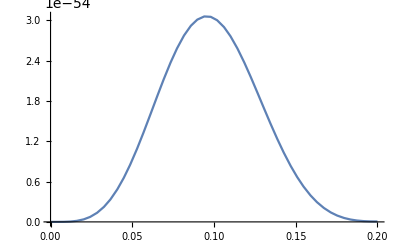

```mathematica
Plot[fplot,{q,0,0.2}]
```

Total predicted number of events for 150 GeV WIMP

```mathematica
2500KilogramDay*NIntegrate[fdEdR[qGeV] GeV*(qGeV GeV/(131 mNucleon))/.MWIMP->(150(*GeV*)),{qGeV,0,10}]
```

34.3331

Total predicted number of events as function of WIMP mass

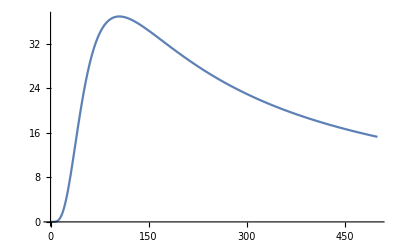

```mathematica
Plot[2500KilogramDay*NIntegrate[fdEdR[qGeV] GeV*(qGeV GeV/(131 mNucleon))/.MWIMP->(M(*GeV*)),{qGeV,0,10}],{M,0,500}]
```